## Initialisation

### fixed parameters

define ionisation potential, electric field amplitude  (intensity), fundamental wavelength...

```mathematica
Ip=0.5;
R = Tan[π/4];
ω = 0.057;
prefactor = ((ⅈ / Sqrt[π])*(2*Ip)^(1/4));(**(Sqrt [2π/ⅈ ])*)
```

### Define fields

electric  field  definition, vector potential, derivative of the action, action, ...

```mathematica
(*Define the electric field function as a 2D vector*)
E1[t_]:={Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2 t],0};
(*Define the vector potential components*)
Ax[tx_]:=-Integrate[E1[t][[1]],t]/. t->tx;
Ay[tx_]:=-Integrate[E1[t][[2]],t]/. t->tx;
(*Define the 2D vector potential A*)
A[tx_]:={Ax[tx],Ay[tx]};

(*Define Sf,Sfunc,DsFunc,D2sFunc,and action in terms of px,Ax,py,and Ay*)
Sf[tk_,p_List]=Integrate[2 (p[[1]]*Ax[t]+p[[2]]*Ay[t])+(Ax[t]^2+Ay[t]^2),t]/. t->tk;
Sfunc[t_,p_List]:=0.5*Sf[t,p]+(0.5*(p[[1]]^2+p[[2]]^2)+Ip)*t;
DsFunc[t_,p_List]:=D[Sfunc[tc,p],tc]/. tc->t;
D2sFunc[t_,p_List]:=ω*D[Sfunc[tz,p],{tz,2}]/. tz->t;
action[t_,p_List]:=Exp[I*Sfunc[t,p]/ω];
```

Part::partd: Part specification p⟦1⟧ is longer than depth of object.

Part::partd: Part specification p⟦2⟧ is longer than depth of object.

### Define the momentum grid

```mathematica
(*Define the range for px and py values*)
pxValues=Range[-2,2,0.1];
pyValues=Range[-2,2,0.1];
Print[Length[pxValues]]
Print[Length[pyValues]]
```

41

41

### Define plotting functions

```mathematica
(*Plot Ex and Ey and roots*)
plotEx:=Quiet[Plot[E1[t][[1]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotEy:=Quiet[Plot[E1[t][[2]],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]];

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

SetDelayed::write: Tag Graphics in ()[filteredTValues_] is Protected.

### Create Grid of Seeds

```mathematica
(*Generate the grid of seeds*)
realMin=-2.133;realMax=4.15;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*Add the specific initial guess to the list of seeds*)
initialGuess=-1.5708+0.8814 I;
listofseeds=Prepend[listofseeds,initialGuess];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;
```

Find  all  the  roots for all px and py values (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_,seeds_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},
(*Find roots*)
allSolutions=Round[t/. Quiet[Table[FindRoot[DsFunc[t,{px,py}]==0,{t,tseed}],{tseed,seeds}]],0.0001];
complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];
(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,{px,py}]]]<=tolerance&&Abs[Im[DsFunc[#,{px,py}]]]<=tolerance&];
{filteredTValues}];
```

## CALCULATION : Saddle Point Solutions

```mathematica
Calculate all the time saddle point solutions value for corresponding px and py below
```

```mathematica
(*Generate results using the precise px and py values*)
results=Table[
generatePlotAndRoots[px,py,listofseeds],
{px,pxValues},{py,pyValues}
];
```

## rearrange data structure of the time arrays & prep them for plotting.

write  a  text  markdown  below  explaining  the  rearranging  data  structure  step  for  newresults, the  same  for  the  following, ts  extended,  valid  data

```mathematica
newResults=
Table[
{(*Calculate pxValue based on the index i*)
pxValue=-2+(i-1)*0.1,
(*Calculate pyValue based on the index j*)
pyValue=-2+(j-1)*0.1,
(*Extract the corresponding results for the current px and py values*)
results[[i,j]]},
(*Iterate over the length of the results list for both i and j*)
{i,Length[results]},{j,Length[results]}
];

(*Get the number of elements in each sub-array at the forth level*)
forthLevelCounts=Length/@#&/@#&/@#&/@newResults;
Print[forthLevelCounts];

(*Flatten the newResults list by one level to get a list of sublists, Map over each sublist in flattenedResults For each sublist elem,join the first two elements with the elements of the nested list inside the third element.*)
tsExtended=Map[Function[{elem},Join[{elem[[1]],elem[[2]]},elem[[3,1]]]],Flatten[newResults,1]];
(*so essentially grabbing px and py and putting them in the same array as the time saddle point solutions ts1,ts2,ts3,ts4 so the array of arrays will look like {{px,py,ts1,ts2,ts3,ts4},repeat for different values of px and py}*)

(*-validData is a list of lists where each sublist contains four elements {Real part of ts,Imaginary part of ts,px,py}.*)
validData=
(*Select elements from the list that satisfy a condition*)
Select[
(*Flatten the nested list into a single list*)
Flatten[
(*Generate a table of values*)
Table[
(*Conditional statement to check if the element is not Null*)
If[tsExtended[[i,j+2]]=!=Null,
{(*Real part of the complex number*)
Re[tsExtended[[i,j+2]]],
(*Imaginary part of the complex number*)
Im[tsExtended[[i,j+2]]],
(*px value*)
tsExtended[[i,1]],
(*py value*)
tsExtended[[i,2]]},
(*If the element is Null,return Nothing*)
Nothing],
(*Iterate over all rows of tsExtended*)
{i,Length[tsExtended]},
(*Iterate over all columns except the first two*)
{j,1,Length[tsExtended[[i]]]-2}],
(*-Flatten at level 1 converts the nested list into a single list*)
1],
(*-Select filters the flattened list to include only the elements where the first element is not Null*)
#[[1]]=!=Null&]

(*Get the number of elements in each sub-array at the first level of Valid Data*)
firstLevelCounts=Length/@validData;
(*Print[firstLevelCounts];*)

(*length of valid data should be equal to the check solutions variable, if not there are missing saddle points as every saddle point px and py should have 4 saddle points*)
checksolutions = Length[pxValues]*Length[pyValues]*4;
Print[checksolutions];
Print[Length[validData]];

(*Extract real and imaginary times from validData*)
realAndImagTimes=validData[[All,1;;2]];
(*[[All,1;;2]] is a part specification that extracts specific elements from each sublist. All indicates that we want to apply the extraction to all sublists in validData.   
1;;2 specifies the range of elements to extract from each sublist. In this case it extracts the first and second element [the real and imaginary parts of the saddle point solutions]*)

(*Generate a 2D heatmap for px and py using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];
(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];
Print[Length[coloredPointsPx]]
(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];
Print[Length[coloredPointsPy]]

(*Define a color function using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-2,2}]];

(*Explanation:
-colorFunction is a function that takes a value (px or py) and maps it to a color.
-ColorData["Rainbow"] returns a function that generates colors from the Rainbow color scheme.
-Rescale[pxOrPy,{-2,2}] rescales the input value pxOrPy from the range {-2,2} to the range {0,1},which is required by ColorData.*)

(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,3]]] applies the color function to the px value (third element) of the i_th sublist in validData.
-Point[validData[[i,1;;2]]] creates a point at the coordinates specified by the real and imaginary parts (first and second elements) of the i-th sublist in validData.
-The result is a list of pairs,where each pair consists of a color and a point.*)

(*Print the length of coloredPointsPx to verify the number of points generated*)
Print[Length[coloredPointsPx]];

(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];

(*Explanation:
-Table is used to generate a list of colored points.
-{i,1,Length[validData]} iterates over all elements in validData.
-colorFunction[validData[[i,4]]] applies the color function to the py value (fourth element) of the i_th sublist in validData.
-Disk[validData[[i,1;;2]],0.05] creates a disk at the coordinates specified by the real and imaginary parts (first and second elements) of the i_th sublist in validData,with a radius of 0.05.
-The result is a list of pairs,where each pair consists of a color and a disk.*)

(*Print the length of coloredPointsPy to verify the number of points generated*)
Print[Length[coloredPointsPy]];
```

{{{-2.,-2.,{3}},{-2.,-1.9,{4}},{-2.,-1.8,{4}},{-2.,-1.7,{4}},{-2.,-1.6,{4}},{-2.,-1.5,{4}},{-2.,-1.4,{4}},{-2.,-1.3,{4}},{-2.,-1.2,{4}},{-2.,-1.1,{4}},{-2.,-1.,{4}},{-2.,-0.9,{4}},{-2.,-0.8,{4}},{-2.,-0.7,{4}},{-2.,-0.6,{4}},{-2.,-0.5,{4}},{-2.,-0.4,{4}},{-2.,-0.3,{4}},{-2.,-0.2,{4}},{-2.,-0.1,{4}},{-2.,0.,{4}},{-2.,0.1,{4}},{-2.,0.2,{4}},{-2.,0.3,{4}},{-2.,0.4,{4}},{-2.,0.5,{4}},{-2.,0.6,{4}},{-2.,0.7,{4}},{-2.,0.8,{4}},{-2.,0.9,{4}},{-2.,1.,{4}},{-2.,1.1,{4}},{-2.,1.2,{4}},{-2.,1.3,{4}},{-2.,1.4,{4}},{-2.,1.5,{4}},{-2.,1.6,{4}},{-2.,1.7,{4}},{-2.,1.8,{4}},{-2.,1.9,{4}},{-2.,2.,{3}}},{{-1.9,-2.,{4}},{-1.9,-1.9,{4}},{-1.9,-1.8,{4}},{-1.9,-1.7,{4}},{-1.9,-1.6,{4}},{-1.9,-1.5,{4}},{-1.9,-1.4,{4}},{-1.9,-1.3,{4}},{-1.9,-1.2,{4}},{-1.9,-1.1,{4}},{-1.9,-1.,{4}},{-1.9,-0.9,{4}},{-1.9,-0.8,{4}},{-1.9,-0.7,{4}},{-1.9,-0.6,{4}},{-1.9,-0.5,{4}},{-1.9,-0.4,{4}},{-1.9,-0.3,{4}},{-1.9,-0.2,{4}},{-1.9,-0.1,{4}},{-1.9,0.,{4}},{-1.9,0.1,{4}},{-1.9,0.2,{4}},{-1.9,0.3,{4}},{-1.9,0.4,{4}},{-1.9,0.5,{4}},{-1.9,0.6,{4}},{-1.9,0.7,{4}},{-1.9,0.8,{4}},{-1.9,0.9,{4}},{-1.9,1.,{4}},{-1.9,1.1,{4}},{-1.9,1.2,{4}},{-1.9,1.3,{4}},{-1.9,1.4,{4}},{-1.9,1.5,{4}},{-1.9,1.6,{4}},{-1.9,1.7,{4}},{-1.9,1.8,{4}},{-1.9,1.9,{4}},{-1.9,2.,{4}}},{{-1.8,-2.,{4}},{-1.8,-1.9,{4}},{-1.8,-1.8,{4}},{-1.8,-1.7,{4}},{-1.8,-1.6,{4}},{-1.8,-1.5,{4}},{-1.8,-1.4,{4}},{-1.8,-1.3,{4}},{-1.8,-1.2,{4}},{-1.8,-1.1,{4}},{-1.8,-1.,{4}},{-1.8,-0.9,{4}},{-1.8,-0.8,{4}},{-1.8,-0.7,{4}},{-1.8,-0.6,{4}},{-1.8,-0.5,{4}},{-1.8,-0.4,{4}},{-1.8,-0.3,{4}},{-1.8,-0.2,{4}},{-1.8,-0.1,{4}},{-1.8,0.,{4}},{-1.8,0.1,{4}},{-1.8,0.2,{4}},{-1.8,0.3,{4}},{-1.8,0.4,{4}},{-1.8,0.5,{4}},{-1.8,0.6,{4}},{-1.8,0.7,{4}},{-1.8,0.8,{4}},{-1.8,0.9,{4}},{-1.8,1.,{4}},{-1.8,1.1,{4}},{-1.8,1.2,{4}},{-1.8,1.3,{4}},{-1.8,1.4,{4}},{-1.8,1.5,{4}},{-1.8,1.6,{4}},{-1.8,1.7,{4}},{-1.8,1.8,{4}},{-1.8,1.9,{4}},{-1.8,2.,{4}}},{{-1.7,-2.,{4}},{-1.7,-1.9,{4}},{-1.7,-1.8,{4}},{-1.7,-1.7,{4}},{-1.7,-1.6,{4}},{-1.7,-1.5,{4}},{-1.7,-1.4,{4}},{-1.7,-1.3,{4}},{-1.7,-1.2,{4}},{-1.7,-1.1,{4}},{-1.7,-1.,{4}},{-1.7,-0.9,{4}},{-1.7,-0.8,{4}},{-1.7,-0.7,{4}},{-1.7,-0.6,{4}},{-1.7,-0.5,{4}},{-1.7,-0.4,{4}},{-1.7,-0.3,{4}},{-1.7,-0.2,{4}},{-1.7,-0.1,{4}},{-1.7,0.,{4}},{-1.7,0.1,{4}},{-1.7,0.2,{4}},{-1.7,0.3,{4}},{-1.7,0.4,{4}},{-1.7,0.5,{4}},{-1.7,0.6,{4}},{-1.7,0.7,{4}},{-1.7,0.8,{4}},{-1.7,0.9,{4}},{-1.7,1.,{4}},{-1.7,1.1,{4}},{-1.7,1.2,{4}},{-1.7,1.3,{4}},{-1.7,1.4,{4}},{-1.7,1.5,{4}},{-1.7,1.6,{4}},{-1.7,1.7,{4}},{-1.7,1.8,{4}},{-1.7,1.9,{4}},{-1.7,2.,{4}}},{{-1.6,-2.,{4}},{-1.6,-1.9,{4}},{-1.6,-1.8,{4}},{-1.6,-1.7,{4}},{-1.6,-1.6,{4}},{-1.6,-1.5,{4}},{-1.6,-1.4,{4}},{-1.6,-1.3,{4}},{-1.6,-1.2,{4}},{-1.6,-1.1,{4}},{-1.6,-1.,{4}},{-1.6,-0.9,{4}},{-1.6,-0.8,{4}},{-1.6,-0.7,{4}},{-1.6,-0.6,{4}},{-1.6,-0.5,{4}},{-1.6,-0.4,{4}},{-1.6,-0.3,{4}},{-1.6,-0.2,{4}},{-1.6,-0.1,{4}},{-1.6,0.,{4}},{-1.6,0.1,{4}},{-1.6,0.2,{4}},{-1.6,0.3,{4}},{-1.6,0.4,{4}},{-1.6,0.5,{4}},{-1.6,0.6,{4}},{-1.6,0.7,{4}},{-1.6,0.8,{4}},{-1.6,0.9,{4}},{-1.6,1.,{4}},{-1.6,1.1,{4}},{-1.6,1.2,{4}},{-1.6,1.3,{4}},{-1.6,1.4,{4}},{-1.6,1.5,{4}},{-1.6,1.6,{4}},{-1.6,1.7,{4}},{-1.6,1.8,{4}},{-1.6,1.9,{4}},{-1.6,2.,{4}}},{{-1.5,-2.,{4}},{-1.5,-1.9,{4}},{-1.5,-1.8,{4}},{-1.5,-1.7,{4}},{-1.5,-1.6,{4}},{-1.5,-1.5,{4}},{-1.5,-1.4,{4}},{-1.5,-1.3,{4}},{-1.5,-1.2,{4}},{-1.5,-1.1,{4}},{-1.5,-1.,{4}},{-1.5,-0.9,{4}},{-1.5,-0.8,{4}},{-1.5,-0.7,{4}},{-1.5,-0.6,{4}},{-1.5,-0.5,{4}},{-1.5,-0.4,{4}},{-1.5,-0.3,{4}},{-1.5,-0.2,{4}},{-1.5,-0.1,{4}},{-1.5,0.,{4}},{-1.5,0.1,{4}},{-1.5,0.2,{4}},{-1.5,0.3,{4}},{-1.5,0.4,{4}},{-1.5,0.5,{4}},{-1.5,0.6,{4}},{-1.5,0.7,{4}},{-1.5,0.8,{4}},{-1.5,0.9,{4}},{-1.5,1.,{4}},{-1.5,1.1,{4}},{-1.5,1.2,{4}},{-1.5,1.3,{4}},{-1.5,1.4,{4}},{-1.5,1.5,{4}},{-1.5,1.6,{4}},{-1.5,1.7,{4}},{-1.5,1.8,{4}},{-1.5,1.9,{4}},{-1.5,2.,{4}}},{{-1.4,-2.,{4}},{-1.4,-1.9,{4}},{-1.4,-1.8,{4}},{-1.4,-1.7,{4}},{-1.4,-1.6,{4}},{-1.4,-1.5,{4}},{-1.4,-1.4,{4}},{-1.4,-1.3,{4}},{-1.4,-1.2,{4}},{-1.4,-1.1,{4}},{-1.4,-1.,{4}},{-1.4,-0.9,{4}},{-1.4,-0.8,{4}},{-1.4,-0.7,{4}},{-1.4,-0.6,{4}},{-1.4,-0.5,{4}},{-1.4,-0.4,{4}},{-1.4,-0.3,{4}},{-1.4,-0.2,{4}},{-1.4,-0.1,{4}},{-1.4,0.,{4}},{-1.4,0.1,{4}},{-1.4,0.2,{4}},{-1.4,0.3,{4}},{-1.4,0.4,{4}},{-1.4,0.5,{4}},{-1.4,0.6,{4}},{-1.4,0.7,{4}},{-1.4,0.8,{4}},{-1.4,0.9,{4}},{-1.4,1.,{4}},{-1.4,1.1,{4}},{-1.4,1.2,{4}},{-1.4,1.3,{4}},{-1.4,1.4,{4}},{-1.4,1.5,{4}},{-1.4,1.6,{4}},{-1.4,1.7,{4}},{-1.4,1.8,{4}},{-1.4,1.9,{4}},{-1.4,2.,{4}}},{{-1.3,-2.,{4}},{-1.3,-1.9,{4}},{-1.3,-1.8,{4}},{-1.3,-1.7,{4}},{-1.3,-1.6,{4}},{-1.3,-1.5,{4}},{-1.3,-1.4,{4}},{-1.3,-1.3,{4}},{-1.3,-1.2,{4}},{-1.3,-1.1,{4}},{-1.3,-1.,{4}},{-1.3,-0.9,{4}},{-1.3,-0.8,{4}},{-1.3,-0.7,{4}},{-1.3,-0.6,{4}},{-1.3,-0.5,{4}},{-1.3,-0.4,{4}},{-1.3,-0.3,{4}},{-1.3,-0.2,{4}},{-1.3,-0.1,{4}},{-1.3,0.,{4}},{-1.3,0.1,{4}},{-1.3,0.2,{4}},{-1.3,0.3,{4}},{-1.3,0.4,{4}},{-1.3,0.5,{4}},{-1.3,0.6,{4}},{-1.3,0.7,{4}},{-1.3,0.8,{4}},{-1.3,0.9,{4}},{-1.3,1.,{4}},{-1.3,1.1,{4}},{-1.3,1.2,{4}},{-1.3,1.3,{4}},{-1.3,1.4,{4}},{-1.3,1.5,{4}},{-1.3,1.6,{4}},{-1.3,1.7,{4}},{-1.3,1.8,{4}},{-1.3,1.9,{4}},{-1.3,2.,{4}}},{{-1.2,-2.,{4}},{-1.2,-1.9,{4}},{-1.2,-1.8,{4}},{-1.2,-1.7,{4}},{-1.2,-1.6,{4}},{-1.2,-1.5,{4}},{-1.2,-1.4,{4}},{-1.2,-1.3,{4}},{-1.2,-1.2,{4}},{-1.2,-1.1,{4}},{-1.2,-1.,{4}},{-1.2,-0.9,{4}},{-1.2,-0.8,{4}},{-1.2,-0.7,{4}},{-1.2,-0.6,{4}},{-1.2,-0.5,{4}},{-1.2,-0.4,{4}},{-1.2,-0.3,{4}},{-1.2,-0.2,{4}},{-1.2,-0.1,{4}},{-1.2,0.,{4}},{-1.2,0.1,{4}},{-1.2,0.2,{4}},{-1.2,0.3,{4}},{-1.2,0.4,{4}},{-1.2,0.5,{4}},{-1.2,0.6,{4}},{-1.2,0.7,{4}},{-1.2,0.8,{4}},{-1.2,0.9,{4}},{-1.2,1.,{4}},{-1.2,1.1,{4}},{-1.2,1.2,{4}},{-1.2,1.3,{4}},{-1.2,1.4,{4}},{-1.2,1.5,{4}},{-1.2,1.6,{4}},{-1.2,1.7,{4}},{-1.2,1.8,{4}},{-1.2,1.9,{4}},{-1.2,2.,{4}}},{{-1.1,-2.,{4}},{-1.1,-1.9,{4}},{-1.1,-1.8,{4}},{-1.1,-1.7,{4}},{-1.1,-1.6,{4}},{-1.1,-1.5,{4}},{-1.1,-1.4,{4}},{-1.1,-1.3,{4}},{-1.1,-1.2,{4}},{-1.1,-1.1,{4}},{-1.1,-1.,{4}},{-1.1,-0.9,{4}},{-1.1,-0.8,{4}},{-1.1,-0.7,{4}},{-1.1,-0.6,{4}},{-1.1,-0.5,{4}},{-1.1,-0.4,{4}},{-1.1,-0.3,{4}},{-1.1,-0.2,{4}},{-1.1,-0.1,{4}},{-1.1,0.,{4}},{-1.1,0.1,{4}},{-1.1,0.2,{4}},{-1.1,0.3,{4}},{-1.1,0.4,{4}},{-1.1,0.5,{4}},{-1.1,0.6,{4}},{-1.1,0.7,{4}},{-1.1,0.8,{4}},{-1.1,0.9,{4}},{-1.1,1.,{4}},{-1.1,1.1,{4}},{-1.1,1.2,{4}},{-1.1,1.3,{4}},{-1.1,1.4,{4}},{-1.1,1.5,{4}},{-1.1,1.6,{4}},{-1.1,1.7,{4}},{-1.1,1.8,{4}},{-1.1,1.9,{4}},{-1.1,2.,{4}}},{{-1.,-2.,{4}},{-1.,-1.9,{4}},{-1.,-1.8,{4}},{-1.,-1.7,{4}},{-1.,-1.6,{4}},{-1.,-1.5,{4}},{-1.,-1.4,{4}},{-1.,-1.3,{4}},{-1.,-1.2,{4}},{-1.,-1.1,{4}},{-1.,-1.,{4}},{-1.,-0.9,{4}},{-1.,-0.8,{4}},{-1.,-0.7,{4}},{-1.,-0.6,{4}},{-1.,-0.5,{4}},{-1.,-0.4,{4}},{-1.,-0.3,{4}},{-1.,-0.2,{4}},{-1.,-0.1,{4}},{-1.,0.,{4}},{-1.,0.1,{4}},{-1.,0.2,{4}},{-1.,0.3,{4}},{-1.,0.4,{4}},{-1.,0.5,{4}},{-1.,0.6,{4}},{-1.,0.7,{4}},{-1.,0.8,{4}},{-1.,0.9,{4}},{-1.,1.,{4}},{-1.,1.1,{4}},{-1.,1.2,{4}},{-1.,1.3,{4}},{-1.,1.4,{4}},{-1.,1.5,{4}},{-1.,1.6,{4}},{-1.,1.7,{4}},{-1.,1.8,{4}},{-1.,1.9,{4}},{-1.,2.,{4}}},{{-0.9,-2.,{4}},{-0.9,-1.9,{4}},{-0.9,-1.8,{4}},{-0.9,-1.7,{4}},{-0.9,-1.6,{4}},{-0.9,-1.5,{4}},{-0.9,-1.4,{4}},{-0.9,-1.3,{4}},{-0.9,-1.2,{4}},{-0.9,-1.1,{4}},{-0.9,-1.,{4}},{-0.9,-0.9,{4}},{-0.9,-0.8,{4}},{-0.9,-0.7,{4}},{-0.9,-0.6,{4}},{-0.9,-0.5,{4}},{-0.9,-0.4,{4}},{-0.9,-0.3,{4}},{-0.9,-0.2,{4}},{-0.9,-0.1,{4}},{-0.9,0.,{4}},{-0.9,0.1,{4}},{-0.9,0.2,{4}},{-0.9,0.3,{4}},{-0.9,0.4,{4}},{-0.9,0.5,{4}},{-0.9,0.6,{4}},{-0.9,0.7,{4}},{-0.9,0.8,{4}},{-0.9,0.9,{4}},{-0.9,1.,{4}},{-0.9,1.1,{4}},{-0.9,1.2,{4}},{-0.9,1.3,{4}},{-0.9,1.4,{4}},{-0.9,1.5,{4}},{-0.9,1.6,{4}},{-0.9,1.7,{4}},{-0.9,1.8,{4}},{-0.9,1.9,{4}},{-0.9,2.,{4}}},{{-0.8,-2.,{4}},{-0.8,-1.9,{4}},{-0.8,-1.8,{4}},{-0.8,-1.7,{4}},{-0.8,-1.6,{4}},{-0.8,-1.5,{4}},{-0.8,-1.4,{4}},{-0.8,-1.3,{4}},{-0.8,-1.2,{4}},{-0.8,-1.1,{4}},{-0.8,-1.,{4}},{-0.8,-0.9,{4}},{-0.8,-0.8,{4}},{-0.8,-0.7,{4}},{-0.8,-0.6,{4}},{-0.8,-0.5,{4}},{-0.8,-0.4,{4}},{-0.8,-0.3,{4}},{-0.8,-0.2,{4}},{-0.8,-0.1,{4}},{-0.8,0.,{4}},{-0.8,0.1,{4}},{-0.8,0.2,{4}},{-0.8,0.3,{4}},{-0.8,0.4,{4}},{-0.8,0.5,{4}},{-0.8,0.6,{4}},{-0.8,0.7,{4}},{-0.8,0.8,{4}},{-0.8,0.9,{4}},{-0.8,1.,{4}},{-0.8,1.1,{4}},{-0.8,1.2,{4}},{-0.8,1.3,{4}},{-0.8,1.4,{4}},{-0.8,1.5,{4}},{-0.8,1.6,{4}},{-0.8,1.7,{4}},{-0.8,1.8,{4}},{-0.8,1.9,{4}},{-0.8,2.,{4}}},{{-0.7,-2.,{4}},{-0.7,-1.9,{4}},{-0.7,-1.8,{4}},{-0.7,-1.7,{4}},{-0.7,-1.6,{4}},{-0.7,-1.5,{4}},{-0.7,-1.4,{4}},{-0.7,-1.3,{4}},{-0.7,-1.2,{4}},{-0.7,-1.1,{4}},{-0.7,-1.,{4}},{-0.7,-0.9,{4}},{-0.7,-0.8,{4}},{-0.7,-0.7,{4}},{-0.7,-0.6,{4}},{-0.7,-0.5,{4}},{-0.7,-0.4,{4}},{-0.7,-0.3,{4}},{-0.7,-0.2,{4}},{-0.7,-0.1,{4}},{-0.7,0.,{4}},{-0.7,0.1,{4}},{-0.7,0.2,{4}},{-0.7,0.3,{4}},{-0.7,0.4,{4}},{-0.7,0.5,{4}},{-0.7,0.6,{4}},{-0.7,0.7,{4}},{-0.7,0.8,{4}},{-0.7,0.9,{4}},{-0.7,1.,{4}},{-0.7,1.1,{4}},{-0.7,1.2,{4}},{-0.7,1.3,{4}},{-0.7,1.4,{4}},{-0.7,1.5,{4}},{-0.7,1.6,{4}},{-0.7,1.7,{4}},{-0.7,1.8,{4}},{-0.7,1.9,{4}},{-0.7,2.,{4}}},{{-0.6,-2.,{4}},{-0.6,-1.9,{4}},{-0.6,-1.8,{4}},{-0.6,-1.7,{4}},{-0.6,-1.6,{4}},{-0.6,-1.5,{4}},{-0.6,-1.4,{4}},{-0.6,-1.3,{4}},{-0.6,-1.2,{4}},{-0.6,-1.1,{4}},{-0.6,-1.,{4}},{-0.6,-0.9,{4}},{-0.6,-0.8,{4}},{-0.6,-0.7,{4}},{-0.6,-0.6,{4}},{-0.6,-0.5,{4}},{-0.6,-0.4,{4}},{-0.6,-0.3,{4}},{-0.6,-0.2,{4}},{-0.6,-0.1,{4}},{-0.6,0.,{4}},{-0.6,0.1,{4}},{-0.6,0.2,{4}},{-0.6,0.3,{4}},{-0.6,0.4,{4}},{-0.6,0.5,{4}},{-0.6,0.6,{4}},{-0.6,0.7,{4}},{-0.6,0.8,{4}},{-0.6,0.9,{4}},{-0.6,1.,{4}},{-0.6,1.1,{4}},{-0.6,1.2,{4}},{-0.6,1.3,{4}},{-0.6,1.4,{4}},{-0.6,1.5,{4}},{-0.6,1.6,{4}},{-0.6,1.7,{4}},{-0.6,1.8,{4}},{-0.6,1.9,{4}},{-0.6,2.,{4}}},{{-0.5,-2.,{4}},{-0.5,-1.9,{4}},{-0.5,-1.8,{4}},{-0.5,-1.7,{4}},{-0.5,-1.6,{4}},{-0.5,-1.5,{4}},{-0.5,-1.4,{4}},{-0.5,-1.3,{4}},{-0.5,-1.2,{4}},{-0.5,-1.1,{4}},{-0.5,-1.,{4}},{-0.5,-0.9,{4}},{-0.5,-0.8,{4}},{-0.5,-0.7,{4}},{-0.5,-0.6,{4}},{-0.5,-0.5,{4}},{-0.5,-0.4,{4}},{-0.5,-0.3,{4}},{-0.5,-0.2,{4}},{-0.5,-0.1,{4}},{-0.5,0.,{4}},{-0.5,0.1,{4}},{-0.5,0.2,{4}},{-0.5,0.3,{4}},{-0.5,0.4,{4}},{-0.5,0.5,{4}},{-0.5,0.6,{4}},{-0.5,0.7,{4}},{-0.5,0.8,{4}},{-0.5,0.9,{4}},{-0.5,1.,{4}},{-0.5,1.1,{4}},{-0.5,1.2,{4}},{-0.5,1.3,{4}},{-0.5,1.4,{4}},{-0.5,1.5,{4}},{-0.5,1.6,{4}},{-0.5,1.7,{4}},{-0.5,1.8,{4}},{-0.5,1.9,{4}},{-0.5,2.,{4}}},{{-0.4,-2.,{4}},{-0.4,-1.9,{4}},{-0.4,-1.8,{4}},{-0.4,-1.7,{4}},{-0.4,-1.6,{4}},{-0.4,-1.5,{4}},{-0.4,-1.4,{4}},{-0.4,-1.3,{4}},{-0.4,-1.2,{4}},{-0.4,-1.1,{4}},{-0.4,-1.,{4}},{-0.4,-0.9,{4}},{-0.4,-0.8,{4}},{-0.4,-0.7,{4}},{-0.4,-0.6,{4}},{-0.4,-0.5,{4}},{-0.4,-0.4,{4}},{-0.4,-0.3,{4}},{-0.4,-0.2,{4}},{-0.4,-0.1,{4}},{-0.4,0.,{4}},{-0.4,0.1,{4}},{-0.4,0.2,{4}},{-0.4,0.3,{4}},{-0.4,0.4,{4}},{-0.4,0.5,{4}},{-0.4,0.6,{4}},{-0.4,0.7,{4}},{-0.4,0.8,{4}},{-0.4,0.9,{4}},{-0.4,1.,{4}},{-0.4,1.1,{4}},{-0.4,1.2,{4}},{-0.4,1.3,{4}},{-0.4,1.4,{4}},{-0.4,1.5,{4}},{-0.4,1.6,{4}},{-0.4,1.7,{4}},{-0.4,1.8,{4}},{-0.4,1.9,{4}},{-0.4,2.,{4}}},{{-0.3,-2.,{4}},{-0.3,-1.9,{4}},{-0.3,-1.8,{4}},{-0.3,-1.7,{4}},{-0.3,-1.6,{4}},{-0.3,-1.5,{4}},{-0.3,-1.4,{4}},{-0.3,-1.3,{4}},{-0.3,-1.2,{4}},{-0.3,-1.1,{4}},{-0.3,-1.,{4}},{-0.3,-0.9,{4}},{-0.3,-0.8,{4}},{-0.3,-0.7,{4}},{-0.3,-0.6,{4}},{-0.3,-0.5,{4}},{-0.3,-0.4,{4}},{-0.3,-0.3,{4}},{-0.3,-0.2,{4}},{-0.3,-0.1,{4}},{-0.3,0.,{4}},{-0.3,0.1,{4}},{-0.3,0.2,{4}},{-0.3,0.3,{4}},{-0.3,0.4,{4}},{-0.3,0.5,{4}},{-0.3,0.6,{4}},{-0.3,0.7,{4}},{-0.3,0.8,{4}},{-0.3,0.9,{4}},{-0.3,1.,{4}},{-0.3,1.1,{4}},{-0.3,1.2,{4}},{-0.3,1.3,{4}},{-0.3,1.4,{4}},{-0.3,1.5,{4}},{-0.3,1.6,{4}},{-0.3,1.7,{4}},{-0.3,1.8,{4}},{-0.3,1.9,{4}},{-0.3,2.,{4}}},{{-0.2,-2.,{4}},{-0.2,-1.9,{4}},{-0.2,-1.8,{4}},{-0.2,-1.7,{4}},{-0.2,-1.6,{4}},{-0.2,-1.5,{4}},{-0.2,-1.4,{4}},{-0.2,-1.3,{4}},{-0.2,-1.2,{4}},{-0.2,-1.1,{4}},{-0.2,-1.,{4}},{-0.2,-0.9,{4}},{-0.2,-0.8,{4}},{-0.2,-0.7,{4}},{-0.2,-0.6,{4}},{-0.2,-0.5,{4}},{-0.2,-0.4,{4}},{-0.2,-0.3,{4}},{-0.2,-0.2,{4}},{-0.2,-0.1,{4}},{-0.2,0.,{4}},{-0.2,0.1,{4}},{-0.2,0.2,{4}},{-0.2,0.3,{4}},{-0.2,0.4,{4}},{-0.2,0.5,{4}},{-0.2,0.6,{4}},{-0.2,0.7,{4}},{-0.2,0.8,{4}},{-0.2,0.9,{4}},{-0.2,1.,{4}},{-0.2,1.1,{4}},{-0.2,1.2,{4}},{-0.2,1.3,{4}},{-0.2,1.4,{4}},{-0.2,1.5,{4}},{-0.2,1.6,{4}},{-0.2,1.7,{4}},{-0.2,1.8,{4}},{-0.2,1.9,{4}},{-0.2,2.,{4}}},{{-0.1,-2.,{4}},{-0.1,-1.9,{4}},{-0.1,-1.8,{4}},{-0.1,-1.7,{4}},{-0.1,-1.6,{4}},{-0.1,-1.5,{4}},{-0.1,-1.4,{4}},{-0.1,-1.3,{4}},{-0.1,-1.2,{4}},{-0.1,-1.1,{4}},{-0.1,-1.,{4}},{-0.1,-0.9,{4}},{-0.1,-0.8,{4}},{-0.1,-0.7,{4}},{-0.1,-0.6,{4}},{-0.1,-0.5,{4}},{-0.1,-0.4,{4}},{-0.1,-0.3,{4}},{-0.1,-0.2,{4}},{-0.1,-0.1,{4}},{-0.1,0.,{4}},{-0.1,0.1,{4}},{-0.1,0.2,{4}},{-0.1,0.3,{4}},{-0.1,0.4,{4}},{-0.1,0.5,{4}},{-0.1,0.6,{4}},{-0.1,0.7,{4}},{-0.1,0.8,{4}},{-0.1,0.9,{4}},{-0.1,1.,{4}},{-0.1,1.1,{4}},{-0.1,1.2,{4}},{-0.1,1.3,{4}},{-0.1,1.4,{4}},{-0.1,1.5,{4}},{-0.1,1.6,{4}},{-0.1,1.7,{4}},{-0.1,1.8,{4}},{-0.1,1.9,{4}},{-0.1,2.,{4}}},{{0.,-2.,{4}},{0.,-1.9,{4}},{0.,-1.8,{4}},{0.,-1.7,{4}},{0.,-1.6,{4}},{0.,-1.5,{4}},{0.,-1.4,{4}},{0.,-1.3,{4}},{0.,-1.2,{4}},{0.,-1.1,{4}},{0.,-1.,{4}},{0.,-0.9,{4}},{0.,-0.8,{4}},{0.,-0.7,{4}},{0.,-0.6,{4}},{0.,-0.5,{4}},{0.,-0.4,{4}},{0.,-0.3,{4}},{0.,-0.2,{4}},{0.,-0.1,{4}},{0.,0.,{4}},{0.,0.1,{4}},{0.,0.2,{4}},{0.,0.3,{4}},{0.,0.4,{4}},{0.,0.5,{4}},{0.,0.6,{4}},{0.,0.7,{4}},{0.,0.8,{4}},{0.,0.9,{4}},{0.,1.,{4}},{0.,1.1,{4}},{0.,1.2,{4}},{0.,1.3,{4}},{0.,1.4,{4}},{0.,1.5,{4}},{0.,1.6,{4}},{0.,1.7,{4}},{0.,1.8,{4}},{0.,1.9,{4}},{0.,2.,{4}}},{{0.1,-2.,{4}},{0.1,-1.9,{4}},{0.1,-1.8,{4}},{0.1,-1.7,{4}},{0.1,-1.6,{4}},{0.1,-1.5,{4}},{0.1,-1.4,{4}},{0.1,-1.3,{4}},{0.1,-1.2,{4}},{0.1,-1.1,{4}},{0.1,-1.,{4}},{0.1,-0.9,{4}},{0.1,-0.8,{4}},{0.1,-0.7,{4}},{0.1,-0.6,{4}},{0.1,-0.5,{4}},{0.1,-0.4,{4}},{0.1,-0.3,{4}},{0.1,-0.2,{4}},{0.1,-0.1,{4}},{0.1,0.,{4}},{0.1,0.1,{4}},{0.1,0.2,{4}},{0.1,0.3,{4}},{0.1,0.4,{4}},{0.1,0.5,{4}},{0.1,0.6,{4}},{0.1,0.7,{4}},{0.1,0.8,{4}},{0.1,0.9,{4}},{0.1,1.,{4}},{0.1,1.1,{4}},{0.1,1.2,{4}},{0.1,1.3,{4}},{0.1,1.4,{4}},{0.1,1.5,{4}},{0.1,1.6,{4}},{0.1,1.7,{4}},{0.1,1.8,{4}},{0.1,1.9,{4}},{0.1,2.,{4}}},{{0.2,-2.,{4}},{0.2,-1.9,{4}},{0.2,-1.8,{4}},{0.2,-1.7,{4}},{0.2,-1.6,{4}},{0.2,-1.5,{4}},{0.2,-1.4,{4}},{0.2,-1.3,{4}},{0.2,-1.2,{4}},{0.2,-1.1,{4}},{0.2,-1.,{4}},{0.2,-0.9,{4}},{0.2,-0.8,{4}},{0.2,-0.7,{4}},{0.2,-0.6,{4}},{0.2,-0.5,{4}},{0.2,-0.4,{4}},{0.2,-0.3,{4}},{0.2,-0.2,{4}},{0.2,-0.1,{4}},{0.2,0.,{4}},{0.2,0.1,{4}},{0.2,0.2,{4}},{0.2,0.3,{4}},{0.2,0.4,{4}},{0.2,0.5,{4}},{0.2,0.6,{4}},{0.2,0.7,{4}},{0.2,0.8,{4}},{0.2,0.9,{4}},{0.2,1.,{4}},{0.2,1.1,{4}},{0.2,1.2,{4}},{0.2,1.3,{4}},{0.2,1.4,{4}},{0.2,1.5,{4}},{0.2,1.6,{4}},{0.2,1.7,{4}},{0.2,1.8,{4}},{0.2,1.9,{4}},{0.2,2.,{4}}},{{0.3,-2.,{4}},{0.3,-1.9,{4}},{0.3,-1.8,{4}},{0.3,-1.7,{4}},{0.3,-1.6,{4}},{0.3,-1.5,{4}},{0.3,-1.4,{4}},{0.3,-1.3,{4}},{0.3,-1.2,{4}},{0.3,-1.1,{4}},{0.3,-1.,{4}},{0.3,-0.9,{4}},{0.3,-0.8,{4}},{0.3,-0.7,{4}},{0.3,-0.6,{4}},{0.3,-0.5,{4}},{0.3,-0.4,{4}},{0.3,-0.3,{4}},{0.3,-0.2,{4}},{0.3,-0.1,{4}},{0.3,0.,{4}},{0.3,0.1,{4}},{0.3,0.2,{4}},{0.3,0.3,{4}},{0.3,0.4,{4}},{0.3,0.5,{4}},{0.3,0.6,{4}},{0.3,0.7,{4}},{0.3,0.8,{4}},{0.3,0.9,{4}},{0.3,1.,{4}},{0.3,1.1,{4}},{0.3,1.2,{4}},{0.3,1.3,{4}},{0.3,1.4,{4}},{0.3,1.5,{4}},{0.3,1.6,{4}},{0.3,1.7,{4}},{0.3,1.8,{4}},{0.3,1.9,{4}},{0.3,2.,{4}}},{{0.4,-2.,{4}},{0.4,-1.9,{4}},{0.4,-1.8,{4}},{0.4,-1.7,{4}},{0.4,-1.6,{4}},{0.4,-1.5,{4}},{0.4,-1.4,{4}},{0.4,-1.3,{4}},{0.4,-1.2,{4}},{0.4,-1.1,{4}},{0.4,-1.,{4}},{0.4,-0.9,{4}},{0.4,-0.8,{4}},{0.4,-0.7,{4}},{0.4,-0.6,{4}},{0.4,-0.5,{4}},{0.4,-0.4,{4}},{0.4,-0.3,{4}},{0.4,-0.2,{4}},{0.4,-0.1,{4}},{0.4,0.,{4}},{0.4,0.1,{4}},{0.4,0.2,{4}},{0.4,0.3,{4}},{0.4,0.4,{4}},{0.4,0.5,{4}},{0.4,0.6,{4}},{0.4,0.7,{4}},{0.4,0.8,{4}},{0.4,0.9,{4}},{0.4,1.,{4}},{0.4,1.1,{4}},{0.4,1.2,{4}},{0.4,1.3,{4}},{0.4,1.4,{4}},{0.4,1.5,{4}},{0.4,1.6,{4}},{0.4,1.7,{4}},{0.4,1.8,{4}},{0.4,1.9,{4}},{0.4,2.,{4}}},{{0.5,-2.,{4}},{0.5,-1.9,{4}},{0.5,-1.8,{4}},{0.5,-1.7,{4}},{0.5,-1.6,{4}},{0.5,-1.5,{4}},{0.5,-1.4,{4}},{0.5,-1.3,{4}},{0.5,-1.2,{4}},{0.5,-1.1,{4}},{0.5,-1.,{4}},{0.5,-0.9,{4}},{0.5,-0.8,{4}},{0.5,-0.7,{4}},{0.5,-0.6,{4}},{0.5,-0.5,{4}},{0.5,-0.4,{4}},{0.5,-0.3,{4}},{0.5,-0.2,{4}},{0.5,-0.1,{4}},{0.5,0.,{4}},{0.5,0.1,{4}},{0.5,0.2,{4}},{0.5,0.3,{4}},{0.5,0.4,{4}},{0.5,0.5,{4}},{0.5,0.6,{4}},{0.5,0.7,{4}},{0.5,0.8,{4}},{0.5,0.9,{4}},{0.5,1.,{4}},{0.5,1.1,{4}},{0.5,1.2,{4}},{0.5,1.3,{4}},{0.5,1.4,{4}},{0.5,1.5,{4}},{0.5,1.6,{4}},{0.5,1.7,{4}},{0.5,1.8,{4}},{0.5,1.9,{4}},{0.5,2.,{4}}},{{0.6,-2.,{4}},{0.6,-1.9,{4}},{0.6,-1.8,{4}},{0.6,-1.7,{4}},{0.6,-1.6,{4}},{0.6,-1.5,{4}},{0.6,-1.4,{4}},{0.6,-1.3,{4}},{0.6,-1.2,{4}},{0.6,-1.1,{4}},{0.6,-1.,{4}},{0.6,-0.9,{4}},{0.6,-0.8,{4}},{0.6,-0.7,{4}},{0.6,-0.6,{4}},{0.6,-0.5,{4}},{0.6,-0.4,{4}},{0.6,-0.3,{4}},{0.6,-0.2,{4}},{0.6,-0.1,{4}},{0.6,0.,{4}},{0.6,0.1,{4}},{0.6,0.2,{4}},{0.6,0.3,{4}},{0.6,0.4,{4}},{0.6,0.5,{4}},{0.6,0.6,{4}},{0.6,0.7,{4}},{0.6,0.8,{4}},{0.6,0.9,{4}},{0.6,1.,{4}},{0.6,1.1,{4}},{0.6,1.2,{4}},{0.6,1.3,{4}},{0.6,1.4,{4}},{0.6,1.5,{4}},{0.6,1.6,{4}},{0.6,1.7,{4}},{0.6,1.8,{4}},{0.6,1.9,{4}},{0.6,2.,{4}}},{{0.7,-2.,{4}},{0.7,-1.9,{4}},{0.7,-1.8,{4}},{0.7,-1.7,{4}},{0.7,-1.6,{4}},{0.7,-1.5,{4}},{0.7,-1.4,{4}},{0.7,-1.3,{4}},{0.7,-1.2,{4}},{0.7,-1.1,{4}},{0.7,-1.,{4}},{0.7,-0.9,{4}},{0.7,-0.8,{4}},{0.7,-0.7,{4}},{0.7,-0.6,{4}},{0.7,-0.5,{4}},{0.7,-0.4,{4}},{0.7,-0.3,{4}},{0.7,-0.2,{4}},{0.7,-0.1,{4}},{0.7,0.,{4}},{0.7,0.1,{4}},{0.7,0.2,{4}},{0.7,0.3,{4}},{0.7,0.4,{4}},{0.7,0.5,{4}},{0.7,0.6,{4}},{0.7,0.7,{4}},{0.7,0.8,{4}},{0.7,0.9,{4}},{0.7,1.,{4}},{0.7,1.1,{4}},{0.7,1.2,{4}},{0.7,1.3,{4}},{0.7,1.4,{4}},{0.7,1.5,{4}},{0.7,1.6,{4}},{0.7,1.7,{4}},{0.7,1.8,{4}},{0.7,1.9,{4}},{0.7,2.,{4}}},{{0.8,-2.,{4}},{0.8,-1.9,{4}},{0.8,-1.8,{4}},{0.8,-1.7,{4}},{0.8,-1.6,{4}},{0.8,-1.5,{4}},{0.8,-1.4,{4}},{0.8,-1.3,{4}},{0.8,-1.2,{4}},{0.8,-1.1,{4}},{0.8,-1.,{4}},{0.8,-0.9,{4}},{0.8,-0.8,{4}},{0.8,-0.7,{4}},{0.8,-0.6,{4}},{0.8,-0.5,{4}},{0.8,-0.4,{4}},{0.8,-0.3,{4}},{0.8,-0.2,{4}},{0.8,-0.1,{4}},{0.8,0.,{4}},{0.8,0.1,{4}},{0.8,0.2,{4}},{0.8,0.3,{4}},{0.8,0.4,{4}},{0.8,0.5,{4}},{0.8,0.6,{4}},{0.8,0.7,{4}},{0.8,0.8,{4}},{0.8,0.9,{4}},{0.8,1.,{4}},{0.8,1.1,{4}},{0.8,1.2,{4}},{0.8,1.3,{4}},{0.8,1.4,{4}},{0.8,1.5,{4}},{0.8,1.6,{4}},{0.8,1.7,{4}},{0.8,1.8,{4}},{0.8,1.9,{4}},{0.8,2.,{4}}},{{0.9,-2.,{4}},{0.9,-1.9,{4}},{0.9,-1.8,{4}},{0.9,-1.7,{4}},{0.9,-1.6,{4}},{0.9,-1.5,{4}},{0.9,-1.4,{4}},{0.9,-1.3,{4}},{0.9,-1.2,{4}},{0.9,-1.1,{4}},{0.9,-1.,{4}},{0.9,-0.9,{4}},{0.9,-0.8,{4}},{0.9,-0.7,{4}},{0.9,-0.6,{4}},{0.9,-0.5,{4}},{0.9,-0.4,{4}},{0.9,-0.3,{4}},{0.9,-0.2,{4}},{0.9,-0.1,{4}},{0.9,0.,{4}},{0.9,0.1,{4}},{0.9,0.2,{4}},{0.9,0.3,{4}},{0.9,0.4,{4}},{0.9,0.5,{4}},{0.9,0.6,{4}},{0.9,0.7,{4}},{0.9,0.8,{4}},{0.9,0.9,{4}},{0.9,1.,{4}},{0.9,1.1,{4}},{0.9,1.2,{4}},{0.9,1.3,{4}},{0.9,1.4,{4}},{0.9,1.5,{4}},{0.9,1.6,{4}},{0.9,1.7,{4}},{0.9,1.8,{4}},{0.9,1.9,{4}},{0.9,2.,{4}}},{{1.,-2.,{4}},{1.,-1.9,{4}},{1.,-1.8,{4}},{1.,-1.7,{4}},{1.,-1.6,{4}},{1.,-1.5,{4}},{1.,-1.4,{4}},{1.,-1.3,{4}},{1.,-1.2,{4}},{1.,-1.1,{4}},{1.,-1.,{4}},{1.,-0.9,{4}},{1.,-0.8,{4}},{1.,-0.7,{4}},{1.,-0.6,{4}},{1.,-0.5,{4}},{1.,-0.4,{4}},{1.,-0.3,{4}},{1.,-0.2,{4}},{1.,-0.1,{4}},{1.,0.,{4}},{1.,0.1,{4}},{1.,0.2,{4}},{1.,0.3,{4}},{1.,0.4,{4}},{1.,0.5,{4}},{1.,0.6,{4}},{1.,0.7,{4}},{1.,0.8,{4}},{1.,0.9,{4}},{1.,1.,{4}},{1.,1.1,{4}},{1.,1.2,{4}},{1.,1.3,{4}},{1.,1.4,{4}},{1.,1.5,{4}},{1.,1.6,{4}},{1.,1.7,{4}},{1.,1.8,{4}},{1.,1.9,{4}},{1.,2.,{4}}},{{1.1,-2.,{4}},{1.1,-1.9,{4}},{1.1,-1.8,{4}},{1.1,-1.7,{4}},{1.1,-1.6,{4}},{1.1,-1.5,{4}},{1.1,-1.4,{4}},{1.1,-1.3,{4}},{1.1,-1.2,{4}},{1.1,-1.1,{4}},{1.1,-1.,{4}},{1.1,-0.9,{4}},{1.1,-0.8,{4}},{1.1,-0.7,{4}},{1.1,-0.6,{4}},{1.1,-0.5,{4}},{1.1,-0.4,{4}},{1.1,-0.3,{4}},{1.1,-0.2,{4}},{1.1,-0.1,{4}},{1.1,0.,{4}},{1.1,0.1,{4}},{1.1,0.2,{4}},{1.1,0.3,{4}},{1.1,0.4,{4}},{1.1,0.5,{4}},{1.1,0.6,{4}},{1.1,0.7,{4}},{1.1,0.8,{4}},{1.1,0.9,{4}},{1.1,1.,{4}},{1.1,1.1,{4}},{1.1,1.2,{4}},{1.1,1.3,{4}},{1.1,1.4,{4}},{1.1,1.5,{4}},{1.1,1.6,{4}},{1.1,1.7,{4}},{1.1,1.8,{4}},{1.1,1.9,{4}},{1.1,2.,{4}}},{{1.2,-2.,{4}},{1.2,-1.9,{4}},{1.2,-1.8,{4}},{1.2,-1.7,{4}},{1.2,-1.6,{4}},{1.2,-1.5,{4}},{1.2,-1.4,{4}},{1.2,-1.3,{4}},{1.2,-1.2,{4}},{1.2,-1.1,{4}},{1.2,-1.,{4}},{1.2,-0.9,{4}},{1.2,-0.8,{4}},{1.2,-0.7,{4}},{1.2,-0.6,{4}},{1.2,-0.5,{4}},{1.2,-0.4,{4}},{1.2,-0.3,{4}},{1.2,-0.2,{4}},{1.2,-0.1,{4}},{1.2,0.,{4}},{1.2,0.1,{4}},{1.2,0.2,{4}},{1.2,0.3,{4}},{1.2,0.4,{4}},{1.2,0.5,{4}},{1.2,0.6,{4}},{1.2,0.7,{4}},{1.2,0.8,{4}},{1.2,0.9,{4}},{1.2,1.,{4}},{1.2,1.1,{4}},{1.2,1.2,{4}},{1.2,1.3,{4}},{1.2,1.4,{4}},{1.2,1.5,{4}},{1.2,1.6,{4}},{1.2,1.7,{4}},{1.2,1.8,{4}},{1.2,1.9,{4}},{1.2,2.,{4}}},{{1.3,-2.,{4}},{1.3,-1.9,{4}},{1.3,-1.8,{4}},{1.3,-1.7,{4}},{1.3,-1.6,{4}},{1.3,-1.5,{4}},{1.3,-1.4,{4}},{1.3,-1.3,{4}},{1.3,-1.2,{4}},{1.3,-1.1,{4}},{1.3,-1.,{4}},{1.3,-0.9,{4}},{1.3,-0.8,{4}},{1.3,-0.7,{4}},{1.3,-0.6,{4}},{1.3,-0.5,{4}},{1.3,-0.4,{4}},{1.3,-0.3,{4}},{1.3,-0.2,{4}},{1.3,-0.1,{4}},{1.3,0.,{4}},{1.3,0.1,{4}},{1.3,0.2,{4}},{1.3,0.3,{4}},{1.3,0.4,{4}},{1.3,0.5,{4}},{1.3,0.6,{4}},{1.3,0.7,{4}},{1.3,0.8,{4}},{1.3,0.9,{4}},{1.3,1.,{4}},{1.3,1.1,{4}},{1.3,1.2,{4}},{1.3,1.3,{4}},{1.3,1.4,{4}},{1.3,1.5,{4}},{1.3,1.6,{4}},{1.3,1.7,{4}},{1.3,1.8,{4}},{1.3,1.9,{4}},{1.3,2.,{4}}},{{1.4,-2.,{4}},{1.4,-1.9,{4}},{1.4,-1.8,{4}},{1.4,-1.7,{4}},{1.4,-1.6,{4}},{1.4,-1.5,{4}},{1.4,-1.4,{4}},{1.4,-1.3,{4}},{1.4,-1.2,{4}},{1.4,-1.1,{4}},{1.4,-1.,{4}},{1.4,-0.9,{4}},{1.4,-0.8,{4}},{1.4,-0.7,{4}},{1.4,-0.6,{4}},{1.4,-0.5,{4}},{1.4,-0.4,{4}},{1.4,-0.3,{4}},{1.4,-0.2,{4}},{1.4,-0.1,{4}},{1.4,0.,{4}},{1.4,0.1,{4}},{1.4,0.2,{4}},{1.4,0.3,{4}},{1.4,0.4,{4}},{1.4,0.5,{4}},{1.4,0.6,{4}},{1.4,0.7,{4}},{1.4,0.8,{4}},{1.4,0.9,{4}},{1.4,1.,{4}},{1.4,1.1,{4}},{1.4,1.2,{4}},{1.4,1.3,{4}},{1.4,1.4,{4}},{1.4,1.5,{4}},{1.4,1.6,{4}},{1.4,1.7,{4}},{1.4,1.8,{4}},{1.4,1.9,{4}},{1.4,2.,{4}}},{{1.5,-2.,{4}},{1.5,-1.9,{4}},{1.5,-1.8,{4}},{1.5,-1.7,{4}},{1.5,-1.6,{4}},{1.5,-1.5,{4}},{1.5,-1.4,{4}},{1.5,-1.3,{4}},{1.5,-1.2,{4}},{1.5,-1.1,{4}},{1.5,-1.,{4}},{1.5,-0.9,{4}},{1.5,-0.8,{4}},{1.5,-0.7,{4}},{1.5,-0.6,{4}},{1.5,-0.5,{4}},{1.5,-0.4,{4}},{1.5,-0.3,{4}},{1.5,-0.2,{4}},{1.5,-0.1,{4}},{1.5,0.,{4}},{1.5,0.1,{4}},{1.5,0.2,{4}},{1.5,0.3,{4}},{1.5,0.4,{4}},{1.5,0.5,{4}},{1.5,0.6,{4}},{1.5,0.7,{4}},{1.5,0.8,{4}},{1.5,0.9,{4}},{1.5,1.,{4}},{1.5,1.1,{4}},{1.5,1.2,{4}},{1.5,1.3,{4}},{1.5,1.4,{4}},{1.5,1.5,{4}},{1.5,1.6,{4}},{1.5,1.7,{4}},{1.5,1.8,{4}},{1.5,1.9,{4}},{1.5,2.,{4}}},{{1.6,-2.,{4}},{1.6,-1.9,{4}},{1.6,-1.8,{4}},{1.6,-1.7,{4}},{1.6,-1.6,{4}},{1.6,-1.5,{4}},{1.6,-1.4,{4}},{1.6,-1.3,{4}},{1.6,-1.2,{4}},{1.6,-1.1,{4}},{1.6,-1.,{4}},{1.6,-0.9,{4}},{1.6,-0.8,{4}},{1.6,-0.7,{4}},{1.6,-0.6,{4}},{1.6,-0.5,{4}},{1.6,-0.4,{4}},{1.6,-0.3,{4}},{1.6,-0.2,{4}},{1.6,-0.1,{4}},{1.6,0.,{4}},{1.6,0.1,{4}},{1.6,0.2,{4}},{1.6,0.3,{4}},{1.6,0.4,{4}},{1.6,0.5,{4}},{1.6,0.6,{4}},{1.6,0.7,{4}},{1.6,0.8,{4}},{1.6,0.9,{4}},{1.6,1.,{4}},{1.6,1.1,{4}},{1.6,1.2,{4}},{1.6,1.3,{4}},{1.6,1.4,{4}},{1.6,1.5,{4}},{1.6,1.6,{4}},{1.6,1.7,{4}},{1.6,1.8,{4}},{1.6,1.9,{4}},{1.6,2.,{4}}},{{1.7,-2.,{4}},{1.7,-1.9,{4}},{1.7,-1.8,{4}},{1.7,-1.7,{4}},{1.7,-1.6,{4}},{1.7,-1.5,{4}},{1.7,-1.4,{4}},{1.7,-1.3,{4}},{1.7,-1.2,{4}},{1.7,-1.1,{4}},{1.7,-1.,{4}},{1.7,-0.9,{4}},{1.7,-0.8,{4}},{1.7,-0.7,{4}},{1.7,-0.6,{4}},{1.7,-0.5,{4}},{1.7,-0.4,{4}},{1.7,-0.3,{4}},{1.7,-0.2,{4}},{1.7,-0.1,{4}},{1.7,0.,{4}},{1.7,0.1,{4}},{1.7,0.2,{4}},{1.7,0.3,{4}},{1.7,0.4,{4}},{1.7,0.5,{4}},{1.7,0.6,{4}},{1.7,0.7,{4}},{1.7,0.8,{4}},{1.7,0.9,{4}},{1.7,1.,{4}},{1.7,1.1,{4}},{1.7,1.2,{4}},{1.7,1.3,{4}},{1.7,1.4,{4}},{1.7,1.5,{4}},{1.7,1.6,{4}},{1.7,1.7,{4}},{1.7,1.8,{4}},{1.7,1.9,{4}},{1.7,2.,{4}}},{{1.8,-2.,{4}},{1.8,-1.9,{4}},{1.8,-1.8,{4}},{1.8,-1.7,{4}},{1.8,-1.6,{4}},{1.8,-1.5,{4}},{1.8,-1.4,{4}},{1.8,-1.3,{4}},{1.8,-1.2,{4}},{1.8,-1.1,{4}},{1.8,-1.,{4}},{1.8,-0.9,{4}},{1.8,-0.8,{4}},{1.8,-0.7,{4}},{1.8,-0.6,{4}},{1.8,-0.5,{4}},{1.8,-0.4,{4}},{1.8,-0.3,{4}},{1.8,-0.2,{4}},{1.8,-0.1,{4}},{1.8,0.,{4}},{1.8,0.1,{4}},{1.8,0.2,{4}},{1.8,0.3,{4}},{1.8,0.4,{4}},{1.8,0.5,{4}},{1.8,0.6,{4}},{1.8,0.7,{4}},{1.8,0.8,{4}},{1.8,0.9,{4}},{1.8,1.,{4}},{1.8,1.1,{4}},{1.8,1.2,{4}},{1.8,1.3,{4}},{1.8,1.4,{4}},{1.8,1.5,{4}},{1.8,1.6,{4}},{1.8,1.7,{4}},{1.8,1.8,{4}},{1.8,1.9,{4}},{1.8,2.,{4}}},{{1.9,-2.,{4}},{1.9,-1.9,{4}},{1.9,-1.8,{4}},{1.9,-1.7,{4}},{1.9,-1.6,{4}},{1.9,-1.5,{4}},{1.9,-1.4,{4}},{1.9,-1.3,{4}},{1.9,-1.2,{4}},{1.9,-1.1,{4}},{1.9,-1.,{4}},{1.9,-0.9,{4}},{1.9,-0.8,{4}},{1.9,-0.7,{4}},{1.9,-0.6,{4}},{1.9,-0.5,{4}},{1.9,-0.4,{4}},{1.9,-0.3,{4}},{1.9,-0.2,{4}},{1.9,-0.1,{4}},{1.9,0.,{4}},{1.9,0.1,{4}},{1.9,0.2,{4}},{1.9,0.3,{4}},{1.9,0.4,{4}},{1.9,0.5,{4}},{1.9,0.6,{4}},{1.9,0.7,{4}},{1.9,0.8,{4}},{1.9,0.9,{4}},{1.9,1.,{4}},{1.9,1.1,{4}},{1.9,1.2,{4}},{1.9,1.3,{4}},{1.9,1.4,{4}},{1.9,1.5,{4}},{1.9,1.6,{4}},{1.9,1.7,{4}},{1.9,1.8,{4}},{1.9,1.9,{4}},{1.9,2.,{4}}},{{2.,-2.,{3}},{2.,-1.9,{4}},{2.,-1.8,{4}},{2.,-1.7,{4}},{2.,-1.6,{4}},{2.,-1.5,{4}},{2.,-1.4,{4}},{2.,-1.3,{4}},{2.,-1.2,{4}},{2.,-1.1,{4}},{2.,-1.,{4}},{2.,-0.9,{4}},{2.,-0.8,{4}},{2.,-0.7,{4}},{2.,-0.6,{4}},{2.,-0.5,{4}},{2.,-0.4,{4}},{2.,-0.3,{4}},{2.,-0.2,{4}},{2.,-0.1,{4}},{2.,0.,{4}},{2.,0.1,{4}},{2.,0.2,{4}},{2.,0.3,{4}},{2.,0.4,{4}},{2.,0.5,{4}},{2.,0.6,{4}},{2.,0.7,{4}},{2.,0.8,{4}},{2.,0.9,{4}},{2.,1.,{4}},{2.,1.1,{4}},{2.,1.2,{4}},{2.,1.3,{4}},{2.,1.4,{4}},{2.,1.5,{4}},{2.,1.6,{4}},{2.,1.7,{4}},{2.,1.8,{4}},{2.,1.9,{4}},{2.,2.,{3}}}}

6724

6720

6720

6720

«2 more identical outputs»

## Plotting Electric Field with Saddle Points Solutions + Complex Plane Time Saddle Points Plot

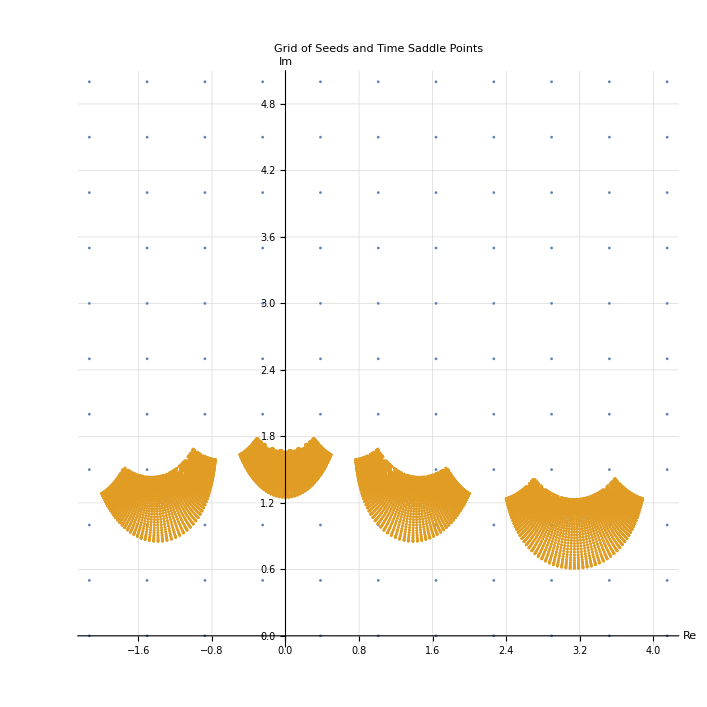

-Graphics3D-

```mathematica
Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
plotRoots=ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large];

Show[plotEx,plotEy,plotRoots,PlotRange->All,PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

Manipulate[
plotData=generatePlotAndRoots[px,py, listofseeds];
filteredTValues=plotData[[1]];
(*Extract time,Ex,and Ey values*)
timeValues=Re[#]&/@filteredTValues;
exValues=E1[#][[1]]&/@timeValues;
eyValues=E1[#][[2]]&/@timeValues;
(*Create root points for plotting*)
rootPoints=Graphics3D[{Red,PointSize[Large],Point[Transpose[{exValues,eyValues,timeValues}]]}];
(*Create 3D plot*)
Show[
ParametricPlot3D[{E1[t][[1]],E1[t][[2]],t},{t,-2.133,4.15},
PlotStyle->{Blue},AxesLabel->{"Electric Field Ex","Electric Field Ey","Time, t"},PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]<>", 3D Electric Field Plot",ImageSize->{1200,600},PlotRange->All],
rootPoints,ImageSize->{1200,600}],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]

(*Plot the grid of seeds and the time saddle points*)
ListPlot[{seedPoints,realAndImagTimes},AxesLabel->{"Re","Im"},PlotRange->{{realMin,realMax},{imagMin,imagMax}},AspectRatio->1,GridLines->Automatic,PlotLabel->"Grid of Seeds and Time Saddle Points"]

(*Plot the 3D graph with color representing py*)ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"4D Data Representation",ImageSize->Large,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Top}]]
```

# Calculating the Yield

```mathematica
(*Selects time saddle point solutions for trajectory A,B,C,D individually and accordingly*)
timeA=Table[validData[[i]],{i,1,Length[validData],4}]
timeB=Table[validData[[i]],{i,2,Length[validData],4}];
timeC=Table[validData[[i]],{i,3,Length[validData],4}];
timeD=Table[validData[[i]],{i,4,Length[validData],4}];
Print[Length[timeA]]

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A*)
psiA =Table[
prefactor*action[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeA[[i,1]]+ⅈ*timeA[[i,2]],{timeA[[i,3]],timeA[[i,4]]}])
],
{i,1,Length[timeA]}]
Print[Length[psiA]]
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj B*)
psiB=Table[
prefactor*action[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeB[[i,1]]+ⅈ*timeB[[i,2]],{timeB[[i,3]],timeB[[i,4]]}])
],
{i,1,Length[timeB]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiC=Table[
prefactor*action[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeC[[i,1]]+ⅈ*timeC[[i,2]],{timeC[[i,3]],timeC[[i,4]]}])
],
{i,1,Length[timeC]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiD=Table[
prefactor*action[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}
]*Sqrt[2π/(ⅈ *D2sFunc[
timeD[[i,1]]+ⅈ*timeD[[i,2]],{timeD[[i,3]],timeD[[i,4]]}])
],
{i,1,Length[timeD]}];

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A+B+C+D*)
totalPsi =psiA+psiB +psiC +psiD;
```

3545

3545

Thread::tdlen: Objects of unequal length in {3.57689×10^-100+2.93855×10^-100 ⅈ,6.65837×10^-60+1.41576×10^-60 ⅈ,3.02109×10^-56+1.0368×10^-56 ⅈ,-1.5746×10^-50-1.86526×10^-50 ⅈ,8.91114×10^-48-1.01687×10^-47 ⅈ,5.32256×10^-45+1.57622×10^-45 ⅈ,7.02586×10^-43+1.54297×10^-42 ⅈ,-5.51253×10^-41+3.82824×10^-40 ⅈ,-1.27464×10^-69+8.76913×10^-70 ⅈ,-4.94792×10^-35-8.33709×10^-35 ⅈ,«3535»}+{«24»-«23» ⅈ,«9»,«3535»}+{«1»}+{-6.17515×10^-97+2.79109×10^-96 ⅈ,3.66405×10^-57+6.97915×10^-57 ⅈ,«8»,«3534»} cannot be combined.

# Plotting The Yield

```mathematica
(*Create data points for each psi*)
dataA=Table[{pxValues[[i]],pyValues[[j]],Abs[psiA[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataB=Table[{pxValues[[i]],pyValues[[j]],Abs[psiB[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataC=Table[{pxValues[[i]],pyValues[[j]],Abs[psiC[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataD=Table[{pxValues[[i]],pyValues[[j]],Abs[psiD[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataTotal=Table[{pxValues[[i]],pyValues[[j]],Abs[totalPsi[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];

(*Flatten the data points*)
dataA=Flatten[dataA,1];
dataB=Flatten[dataB,1];
dataC=Flatten[dataC,1];
dataD=Flatten[dataD,1];
dataTotal=Flatten[dataTotal,1];

(*Create 3D plots for each psi*)
ListLinePlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->{1200,600}]
```